```mathematica
In this page I want to make the animation of projectile-motion.
```

```mathematica
m=0.14;
v=45;
θ=π/3;
g=9.829878576;
b=0.033
```

0.033

```mathematica
se3[x_]=(g m^2 Log[1-(b x Sec[θ])/(m v)])/b^2+(g x m Sec[θ])/(b v)+x Tan[θ];
se4[x_]=1/b^2(m (b v Sin[θ]+g m (1-Log[1-(b x Sec[θ])/(m v)]-2 Log[1+(b v Sin[θ])/(g m)]+(g m^2 v Cos[θ])/((b x-m v Cos[θ]) (g m+b v Sin[θ])))))
```

128.558 (1.28605+1.37618 (-0.319701+1.62832/(-3.15+0.033 x)-Log[1-0.0104762 x]))

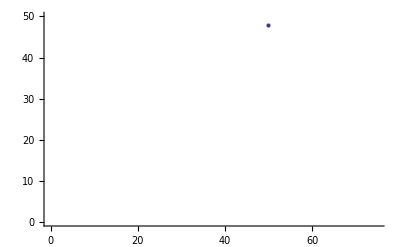
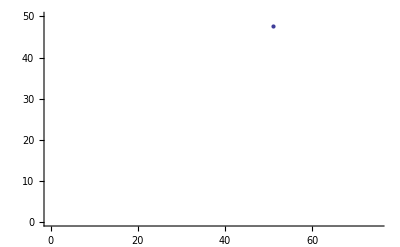
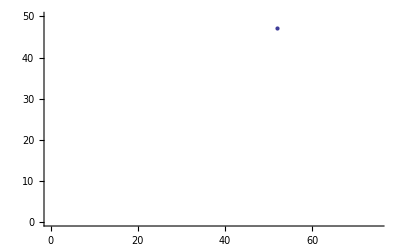
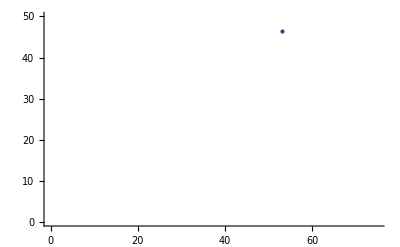
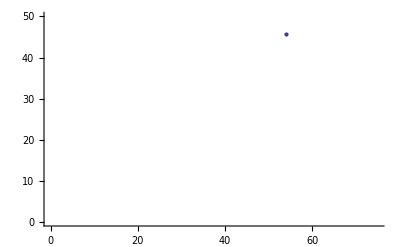
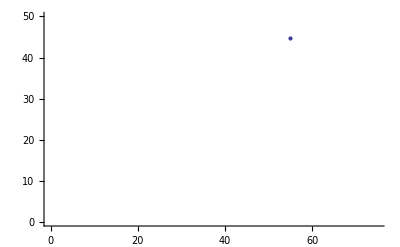
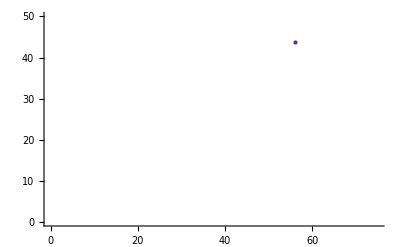
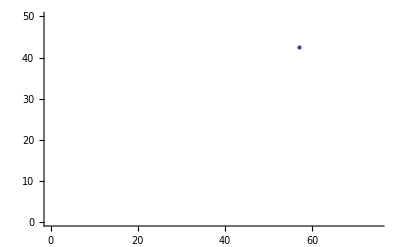

```mathematica
Table[ListPlot[{{x,se3[x]}},PlotRange->{{0,75},{0,50}}],{x,1,50,1}];
Table[ListPlot[{{x,se4[x]}},PlotRange->{{0,75},{0,50}}],{x,50,70,1}]
```